## Cifrario SKINNY-64

```mathematica
(*Cifratura e decifratura*)
Sbox="C6901A2B385D4E7F";
S[x_]:=IntegerDigits[FromDigits[Sbox,16],16,16][[x+1]];
SubCells[state_]:=Map[S,state,{2}]
AddRoundTweakey[state_,key_]:=Join[MapThread[BitXor[#1,#2]&,{state[[1;;2]],key[[1;;2]]},2],state[[3;;4]]]
Perm[state_, perm_]:=Partition[Flatten[state][[perm]],4]
ShiftRows[state_]:=Perm[state, {1,2,3,4,8,5,6,7,11,12,9,10,14,15,16,13}]
MixColumns[state_]:=Transpose[Table[{BitXor[state[[1,j]],state[[3,j]],state[[4,j]]],state[[1,j]],BitXor[state[[2,j]],state[[3,j]]],BitXor[state[[1,j]],state[[3,j]]]}, {j, 4}]]
AddConstants[state_,constants_]:=MapThread[BitXor[#1,#2]&,{state, constants}, 2];

GenKey[key_,Nr_]:=NestList[Perm[ #, {10,16,9,14,11,15,13,12,1,2,3,4,5,6,7,8}]&, key, Nr-1]
rc={0,0,0,0,0,0};
LFSR[rc_, Nr_]:=NestList[{BitXor[#[[6]],#[[5]],1],#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&, rc,  Nr][[2;;]];
RoundConstant[rc_]:=Module[{c0, c1}, 
						c0=FromDigits[{rc[[4]],rc[[3]],rc[[2]],rc[[1]]},2];
						c1=FromDigits[{0,0,rc[[6]],rc[[5]]},2];
						{{c0,0, 0, 0},{c1,0,0,0},{2,0,0,0},{0,0,0,0}}]
GenConstant[rc_]:= Map[RoundConstant, rc];

SkinnyRound[state_, {roundkey_, constants_}]:=Module[{s}, 
													s=state;s=SubCells[s]; s=AddConstants[s, constants]; s=AddRoundTweakey[s, roundkey]; s=ShiftRows[s]; s=MixColumns[s]];
Encryption[plaintext_, roundkeys_, constants_]:=Fold[SkinnyRound, plaintext, Transpose[{roundkeys, constants}]]
```

```mathematica
MixColumnsInv[state_]:=Transpose[Table[{state[[2,j]],BitXor[state[[2,j]],state[[3,j]],state[[4,j]]],BitXor[state[[2,j]],state[[4,j]]],BitXor[state[[1,j]],state[[4,j]]]}, {j, 4}]]
ShiftRowsInv[state_]:=Perm[state, {1,2,3,4,6,7,8,5,11,12,9,10,16,13,14,15}]
AddRoundTweakeyInv[state_, key_]:=AddRoundTweakey[state, key]
AddConstantsInv[state_,constants_]:=AddConstants[state, constants]
Sinv[x_]:=(Ordering[IntegerDigits[FromDigits[Sbox,16],16,16]]-1)[[x+1]]
SubCellsInv[state_]:=Map[Sinv, state, {2}]
SkinnyRoundInv[state_, {roundkey_, constants_}]:=Module[{s},
														s=state; s=MixColumnsInv[s];  s=ShiftRowsInv[s]; s=AddRoundTweakeyInv[s,roundkey];
														s=AddConstantsInv[s,constants]; s=SubCellsInv[s]]
Decryption[ciphertext_, roundkeys_, constants_]:=Fold[SkinnyRoundInv, ciphertext, Reverse[Transpose[{roundkeys,constants}]]]
```

```mathematica
(*Verifica di cifratura e decifratura*)
Nr=6;
plaintext="e285fa146b2c7de3";
key={{13,8,12,2},{8,5,9,5},{3,4,1,4},{8,12,12,9}};
roundkeys=GenKey[key,Nr];
constants=GenConstant[LFSR[rc, Nr]];
ciphertext=Encryption[Partition[IntegerDigits[FromDigits[plaintext,16],16,16],4],roundkeys,constants]
Decryption[ciphertext, roundkeys,constants]
```

{{5,3,13,8},{10,5,8,14},{4,4,15,12},{1,14,7,10}}

{{14,2,8,5},{15,10,1,4},{6,11,2,12},{7,13,14,3}}

```mathematica
(*Test vector, con Nr=32*)
Nr=32;
key="f5269826fc681238";
plaintext0="06034f957724d19d";
ciphertext0="bb39dfb2429b8ac7";
constants=GenConstant[LFSR[rc, Nr]];
roundkeys=GenKey[Partition[IntegerDigits[FromDigits[key,16],16,16],4],Nr];
ciphertext=Encryption[Partition[IntegerDigits[FromDigits[plaintext0,16],16,16],4],roundkeys,constants];
Print["La cifratura coincide con il vettore di prova: ", IntegerString[FromDigits[Flatten[ciphertext],16],16,16]==ciphertext0]
Print["La decifratura coincide con il plaintext originale: ",IntegerString[FromDigits[Flatten[Decryption[ciphertext, roundkeys,constants]],16],16,16]==plaintext0]
```

La cifratura coincide con il vettore di prova: True

La decifratura coincide con il plaintext originale: True

```mathematica
Nr=6;
Genkey[key_]:=GenKey[key,Nr];
```

## Attacco originale MITM

```mathematica
(*Prova con solo 6 nibble della chiave incogniti*)
E1[P_, roundkeys_]:=Encryption[P, roundkeys[[1;;3]], constants[[1;;3]]];
D1[C_, roundkeys_]:=Decryption[C, roundkeys[[4;;6]], constants[[4;;6]]];

CandKeys[p_,c_,k_]:=Module[{rk,e1,e2},
				rk=GenKey[k];
				e1=E1[p,rk];
				e2=D1[c,rk]; 
				If[e1==e2, k]];
p=RandomInteger[{0,15},{4,4}];
c=Encryption[p,roundkeys,constants];
keys=Tuples[Range[0,15],6];
keys=Map[Join[#,Flatten[key][[7;;]]]&,keys];
{tempo1,keys}=AbsoluteTiming[DeleteCases[Map[CandKeys[p,c,Partition[#,4]]&,keys],Null]]
```

{9516.65,{{{13,8,12,2},{8,5,9,5},{3,4,1,4},{8,12,12,9}}}}

```mathematica
codebook=Table[{P=RandomInteger[{0,15},{4,4}],Encryption[P,GenKey[key],constants]},{i,100}];
KeyVerify[k_]:=Module[{rk=GenKey[k]},AllTrue[codebook,Encryption[#[[1]],rk,constants]==#[[2]]&]];
{tempo2,keyfind}=AbsoluteTiming[Map[If[KeyVerify[#]==True,#]&,keys]]; 
keyfind=Partition[Flatten[keyfind],4];
Print["La chiave trovata è ", keyfind]
keyfind==key 
Print["L'attacco è stato completato in ", tempo1+tempo2 ," secondi"]
```

La chiave trovata è {{13,8,12,2},{8,5,9,5},{3,4,1,4},{8,12,12,9}}

True

L'attacco è stato completato in 9516.7 secondi

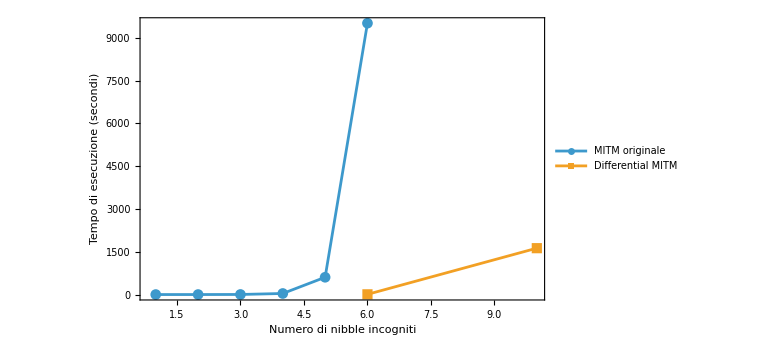

```mathematica
ListLinePlot[{{{1,0.00985},{2,0.16339},{3,2.65117},{4,37.0234},{5,606.097},{6,9516.7}},{{6,7.1237},{10,1626.1565}}},FrameLabel->{"Numero di nibble incogniti","Tempo di esecuzione (secondi)"},Frame->True,PlotRange->All,PlotLegends->{"MITM originale","Differential MITM"},PlotMarkers->Automatic,ImageSize->Large, AxesStyle->Directive[13]]
```

## Attacco differenziale MITM

```mathematica
Ein[P_, roundkeys_]:=Encryption[P, roundkeys[[1;;2]], constants[[1;;2]]];
Din[C_, roundkeys_]:=Decryption[C, roundkeys[[1;;2]], constants[[1;;2]]];
Em[P_, roundkeys_]:=Encryption[P, roundkeys[[3;;4]], constants[[3;;4]]];
Dm[C_, roundkeys_]:=Decryption[C, roundkeys[[3;;4]], constants[[3;;4]]];
Eout[P_, roundkeys_]:=Encryption[P, roundkeys[[5;;6]], constants[[5;;6]]];
Dout[C_, roundkeys_]:=Decryption[C, roundkeys[[5;;6]], constants[[5;;6]]];
```

```mathematica
(*Costruzione della DDT*)
DDT:=Table[Table[Count[Table[BitXor[S[x],S[BitXor[x,dx]]],{x,0,15}],dy],{dy,0,15}], {dx,0,15}];
MatrixForm[DDT]
```

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 0 | 0
0 | 4 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
0 | 0 | 4 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 4 | 2 | 2 | 0 | 0
0 | 0 | 4 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 4 | 0 | 2 | 2 | 0 | 0
0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 2 | 0
0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2
0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2
0 | 0 | 0 | 0 | 0 | 4 | 4 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0
0 | 4 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2
0 | 0 | 4 | 0 | 0 | 0 | 2 | 2 | 4 | 0 | 0 | 0 | 0 | 0 | 2 | 2
0 | 0 | 4 | 0 | 0 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 2 | 2
0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | 0 | 2 | 2 | 0
0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 2 | 0 | 0 | 2)

```mathematica
X={{2,15,5,13},{6,12,5,4},{8,7,7,4},{9,8,14,0}};
dX={{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}};
X'=BitXor[X,dX];
Prob[dx_,dy_]:=DDT[[dx+1,dy+1]]/16;
LinearRound[s_,constant_]:=MixColumns[ShiftRows[AddConstants[s,constant]]];
TrailProb[x1_,x2_]:=Module[{dx,y1,y2,dy,p1},
							dx=BitXor[x1,x2];
							y1=SubCells[x1];
							y2=SubCells[x2];
							dy=BitXor[y1,y2];
							p1=Apply[Times,Flatten[MapThread[Prob,{dx,dy},2]]];
							{y1,y2,p1}]
{y1,y2,p1}=TrailProb[X,X'];
{z1,z2,p2}=TrailProb[LinearRound[y1,constants[[3]]], LinearRound[y2,constants[[3]]]];
prob=p1*p2
dy=BitXor[LinearRound[z1,constants[[4]]],LinearRound[z2,constants[[4]]]]
```

1/16

{{5,0,0,0},{0,0,0,0},{5,0,0,0},{5,0,0,0}}

```mathematica
(*Costruzione delle chiavi kin e kout per la fase forward e backward dell'attacco*)
GenKin[e_,Er_,Dr_,dx_]:=Module[{X,key,y1,z1,y2,z2},
				X=RandomInteger[{0,15},{4,4}];
				key=RandomInteger[{0,15},{4,4}];
				y1=Er[X,GenKey[key]];
				z1=Dr[BitXor[y1,dx],GenKey[key]];
				y2=Er[X,GenKey[BitXor[key,e]]];
				z2=Dr[BitXor[y2,dx],GenKey[BitXor[key,e]]];
				If[z1!=z2, 1, 0]]
kin=Table[Max@@Table[GenKin[Partition[IdentityMatrix[16][[i]],4],Ein,Din,dX],{100}],{i,1,16}]
posin=Flatten[Position[kin,1]];
kout=Table[Max@@Table[GenKin[ Partition[IdentityMatrix[16][[i]],4],Dout,Eout,dy],{100}],{i,1,16}]
posout=Flatten[Position[kout,1]];
(*Impongo alcuni nibble della chiave per diminuire il costo computazionale*)
posout={8,9,10};
kout[[{12,13,16}]]={4,8,9};

comb=Tuples[Range[0,15],Length[posin]];
kin=Map[Partition[ReplacePart[kin,Thread[posin->#]],4]&,comb];
(*comb=Tuples[Range[0,15],Length[posout]];*)
kout=Map[Partition[ReplacePart[kout,Thread[posout->#]],4]&,comb];
```

{1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,1,1,1,0,1,1,0,0,1}

```mathematica
structure=Table[{P=RandomInteger[{0,15},{4,4}],Encryption[P,GenKey[key],constants]},{i,1/prob}];
HashTableEnc[p_,k_]:=GroupBy[Transpose[{Map[Encryption[#,roundkeys, constants]&,p],k}],First->Last];
HashTableDec[p_,k_]:=GroupBy[Transpose[{p,k}],First->Last];
GenHashTable[p_,k_, E1_,E2_,delta_,HashTable_,pos_]:=Module[{keylist,q,ht,k0},
						keylist=Map[GenKey,k];
						q=Map[E2[BitXor[E1[p,#],delta],#]&,keylist];
						k0=Map[Partition[ReplacePart[Flatten[#],Thread[pos->-1]],4]&,k];
						ht=HashTable[q,k0]];
MergeKeys[k1_,k2_]:=Module[{pairs},
							pairs=Transpose[{Flatten[k1],Flatten[k2]}];
							If[AnyTrue[pairs,#[[1]]!=-1&&#[[2]]!=-1&&#[[1]]!=#[[2]]&],Nothing,Partition[pairs/. {{-1,x_}->x,{x_,-1}->x,{x_,x_}->x},4]]]

CandidateKeys[NumKey0_,{p_,c_}]:=Module[{ht1,ht2,m,keys},
						ht1=GenHashTable[p,kin,Ein,Din,dX,HashTableEnc,Flatten[Position[Flatten[kin[[-1]]],0]]];
						ht2=GenHashTable[c,kout,Dout,Eout,dy,HashTableDec,Flatten[Position[Flatten[kout[[-1]]],0]]];
						m=Flatten[Intersection[Keys[ht1],Keys[ht2]],1];
						If[m=={}, Return[NumKey0]];
						keys=Flatten[Table[MergeKeys[k1,k2],{k1,ht1[m]},{k2,ht2[m]}],1];
						Merge[{NumKey0,Counts[keys]},Total]];
{tempo1,keys}=AbsoluteTiming[Keys[Sort[Fold[CandidateKeys,<||>,structure],Greater]]]
```

{80.1646,{{{13,10,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{13,10,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{13,3,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{13,1,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{11,10,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{11,3,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,5},{14,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,5},{14,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,4},{14,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,4},{14,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,1},{14,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,1},{14,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,0},{14,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,0},{14,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,5},{14,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,5},{14,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,5},{3,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,5},{3,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,4},{14,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,4},{14,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,4},{3,12,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,4},{3,4,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,1},{14,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,1},{14,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,1},{3,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,1},{3,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,0},{14,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,0},{14,6,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,0},{3,14,-1,4},{8,-1,-1,9}},{{11,1,-1,-1},{-1,-1,6,0},{3,6,-1,4},{8,-1,-1,9}}}}

```mathematica
(*Ricerca esaustiva tra le chiavi candidate*)
codebook=Table[{P=RandomInteger[{0,15},{4,4}],Encryption[P,GenKey[key],constants]},{i,100}];
KeyVerify[k_]:=Module[{rk=GenKey[Partition[k,4]]},
					AllTrue[codebook,Encryption[#[[1]],rk,constants]==#[[2]]&]];
BruteForce[k0_,pos_,comb_]:=Catch[Scan[(With[{key=ReplacePart[k0,Thread[pos->#]]},If[KeyVerify[key],Throw[key]]])&,comb];Null];
pos=Flatten[Position[Flatten[keys[[1]]],-1]];
(*Impongo alcuni nibble della chiave per diminuire il costo computazionale*)
keys=Map[Partition[ReplacePart[Flatten[#],Thread[{11,14,15}->{1,12,12}]],4]&,keys];
pos=Complement[pos,{11,14,15}];
comb=Tuples[Range[0,15],Length[pos]];
{tempo2,keyfind}=AbsoluteTiming[Catch[Scan[(With[{ck=BruteForce[Flatten[#],pos,comb]},If[ck=!=Null,Throw[Partition[ck,4]]]])&,keys]]];
Print["La chiave trovata dall'attacco è: ",keyfind]
keyfind==key
Print["Il tempo impiegato dall'attacco è: ",tempo1+tempo2]
```

La chiave trovata dall'attacco è: {{13,8,12,2},{8,5,9,5},{3,4,1,4},{8,12,12,9}}

True

Il tempo impiegato dall'attacco è: 1626.16

### Confronto in tempo dell’attacco con o senza ordinamento dell’insieme delle chiavi

```mathematica
structure=Table[{P=RandomInteger[{0,15},{4,4}],Encryption[P,GenKey[key],constants]},{i,1/prob}]; 
{tempo1,keys}=AbsoluteTiming[Keys[Sort[Fold[CandidateKeys,<||>,structure],Greater]]]
(*La posizione della chiave corretta è 82*)
```

{84.6325,{{{13,14,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}}}}

```mathematica
(*Ricerca esaustiva tra le chiavi candidate*)
codebook=Table[{P=RandomInteger[{0,15},{4,4}],Encryption[P,GenKey[key],constants]},{i,100}]; (*Per fare il confronto ho usato la stessa structure e lo stesso codebook*)
pos=Flatten[Position[Flatten[keys[[1]]],-1]];
(*Impongo alcuni nibble della chiave per diminuire il costo computazionale*)
keys=Map[Partition[ReplacePart[Flatten[#],Thread[{11,14,15}->{1,12,12}]],4]&,keys];
pos=Complement[pos,{11,14,15}];
comb=Tuples[Range[0,15],Length[pos]];
{tempo2,keyfind}=AbsoluteTiming[Catch[Scan[(With[{ck=BruteForce[Flatten[#],pos,comb]},If[ck=!=Null,Throw[Partition[ck,4]]]])&,keys]]];
Print["La chiave trovata dall'attacco è: ",keyfind]
keyfind==key
Print["Il tempo impiegato dall'attacco è: ",tempo1+tempo2]
```

La chiave trovata dall'attacco è: {{13,8,12,2},{8,5,9,5},{3,4,1,4},{8,12,12,9}}

True

Il tempo impiegato dall'attacco è: 2878.88

```mathematica
(*Costruzione dell'insieme delle chiavi candidate senza ordinamento*)
CandidateKeys0[keys0_,{p_,c_}]:=Module[{ht1,ht2,m,keys},
									ht1=GenHashTable[p,kin,Ein,Din,dX,HashTableEnc,Flatten[Position[Flatten[kin[[-1]]],0]]];
									ht2=GenHashTable[c,kout,Dout,Eout,dy,HashTableDec,Flatten[Position[Flatten[kout[[-1]]],0]]];
									m=Flatten[Intersection[Keys[ht1],Keys[ht2]],1];
									If[m=={},Return[keys0]];
									keys=DeleteDuplicates[Flatten[Table[MergeKeys[k1,k2],{k1,ht1[m]},{k2,ht2[m]}],1]];
									Union[keys0,keys]];
{tempo1,keys}=AbsoluteTiming[Fold[CandidateKeys0,{},structure]]
(*La posizione della chiave corretta è 173*)
```

{81.0926,{{{11,8,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{11,8,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{11,14,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{13,8,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,0,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,2,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,9,5},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,0},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{3,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{3,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{12,6,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,1},{12,14,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,4},{12,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{3,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{3,12,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{12,4,-1,4},{8,-1,-1,9}},{{13,14,-1,-1},{-1,-1,11,5},{12,12,-1,4},{8,-1,-1,9}}}}

```mathematica
(*Ricerca esaustiva tra le chiavi candidate*)
pos=Flatten[Position[Flatten[keys[[1]]],-1]];
(*Impongo alcuni nibble della chiave per diminuire il costo computazionale*)
keys=Map[Partition[ReplacePart[Flatten[#],Thread[{11,14,15}->{1,12,12}]],4]&,keys];
pos=Complement[pos,{11,14,15}];
comb=Tuples[Range[0,15],Length[pos]];
{tempo2,keyfind}=AbsoluteTiming[Catch[Scan[(With[{ck=BruteForce[Flatten[#],pos,comb]},If[ck=!=Null,Throw[Partition[ck,4]]]])&,keys]]];
Print["La chiave trovata dall'attacco è: ",keyfind]
keyfind==key
Print["Il tempo impiegato dall'attacco è: ",tempo1+tempo2]
```

La chiave trovata dall'attacco è: {{13,8,12,2},{8,5,9,5},{3,4,1,4},{8,12,12,9}}

True

Il tempo impiegato dall'attacco è: 6062.23